```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
orbit=2685;
```

## Initialize J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"18:28:28.364","18:28:30.871","18:28:33.378","18:28:35.885","18:28:38.392","18:28:40.899","18:28:43.406","18:28:45.913","18:28:48.420","18:28:50.927","18:28:53.435","18:28:55.942","18:28:58.449","18:29:00.956","18:29:03.463","18:29:05.970","18:29:08.477","18:29:10.984","18:29:13.491","18:29:15.998","18:29:18.505","18:29:21.013","18:29:23.520","18:29:26.027","18:29:28.534","18:29:31.041","18:29:33.548","18:29:36.055","18:29:38.563","18:29:41.070","18:29:43.577","18:29:46.084","18:29:48.591","18:29:51.099","18:29:53.606","18:29:56.113","18:29:58.620","18:30:01.128","18:30:03.635","18:30:06.142","18:30:08.649","18:30:11.157","18:30:13.664","18:30:16.171","18:30:18.679","18:30:21.186","18:30:23.693","18:30:26.200","18:30:28.708","18:30:31.215"};
pots={203.84,141.12,101.92,117.60,117.60,86.24,86.24,141.12,172.48,117.60,141.12,117.60,141.12,172.48,235.20,203.84,172.48,172.48,203.84,203.84,172.48,117.60,117.60,117.60,117.60,141.12,235.20,203.84,235.20,235.20,203.84,172.48,203.84,172.48,203.84,203.84,282.24,235.20,282.24,282.24,203.84,141.12,117.60,86.24,101.92,101.92,101.92,86.24,117.60,101.92};
curs={0.731,0.560,0.391,0.545,0.503,0.254,0.265,0.648,0.786,0.641,0.622,0.633,1.021,1.070,1.488,1.200,0.932,1.197,1.077,1.014,0.699,0.778,0.595,0.611,0.646,0.910,1.304,1.164,1.270,1.155,1.068,0.822,1.048,1.112,1.283,0.972,1.495,1.262,1.342,1.328,0.884,0.678,0.588,0.302,0.178,0.110,0.124,0.121,0.111,0.135};
curErrs={0.047,0.040,0.038,0.031,0.032,0.020,0.019,0.025,0.027,0.024,0.022,0.021,0.024,0.030,0.033,0.033,0.029,0.040,0.009,0.008,0.007,0.008,0.007,0.007,0.007,0.009,0.010,0.010,0.011,0.010,0.010,0.009,0.010,0.011,0.011,0.011,0.013,0.012,0.013,0.013,0.010,0.009,0.009,0.008,0.005,0.005,0.005,0.005,0.006,0.006};
jes={0.229,0.177,0.131,0.163,0.158,0.109,0.113,0.173,0.219,0.176,0.162,0.153,0.263,0.303,0.453,0.346,0.274,0.342,0.323,0.281,0.200,0.200,0.156,0.167,0.165,0.236,0.367,0.315,0.385,0.339,0.305,0.226,0.303,0.282,0.351,0.274,0.459,0.356,0.406,0.388,0.221,0.158,0.136,0.087,0.069,0.053,0.057,0.059,0.053,0.059};
jeErrs={0.017,0.040,0.014,0.014,0.030,0.010,0.021,0.011,0.009,0.006,0.015,0.005,0.009,0.013,0.018,0.016,0.011,0.018,0.145,0.142,0.019,0.026,0.012,0.010,0.053,0.024,0.072,0.330,0.059,0.604,0.092,0.177,1.872,0.284,0.070,0.214,0.040,0.032,0.020,0.065,0.104,0.124,0.196,0.035,0.004,0.003,0.046,0.005,0.002,0.020};
gaussbulkEs={150.70,167.65,117.60,164.34,142.16,111.82,117.60,177.85,210.43,104.19,116.02,170.49,194.01,203.17,253.53,267.16,163.16,168.12,210.39,171.66,123.99,149.93,126.40,172.48,172.48,177.78,260.04,282.24,173.85,304.65,192.62,204.29,230.65,232.70,253.11,147.10,264.87,196.34,307.82,172.48,141.55,155.16,91.20,117.60,111.80,81.75,117.60,115.87,58.80,113.39};
kappabulkEs={235.20,111.71,78.40,164.68,168.10,102.12,117.60,198.48,234.55,151.06,168.78,126.49,203.84,215.00,280.05,247.65,203.62,187.68,252.51,242.75,234.84,86.25,123.11,169.81,155.92,182.14,207.30,142.03,300.12,322.56,195.43,187.44,189.14,175.10,236.68,170.00,270.74,182.10,297.99,230.38,148.40,124.31,90.20,58.80,66.70,117.60,116.69,117.60,102.23,117.60};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=1;ind1End=40;ind1Init=38;ind2Init=44;(*Jim alt?*)
```

```mathematica
ind1Start=1;ind1End=15;ind1Init=5;ind2Init=16;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[5,16];
```

```mathematica
inds1=Range[11,24];
```

```mathematica
inds2=Range[1,25];
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=10;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=300;
```

```mathematica
minJ=0;maxJ=2.0;
```

```mathematica
minJe=0;maxJe=0.6;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb2685__JVFit__inds_5-16.png,Orb2685__JeVFit__inds_5-16.png,Orb2685__combJVJeVFit__inds_5-16.png}

### J-V plot

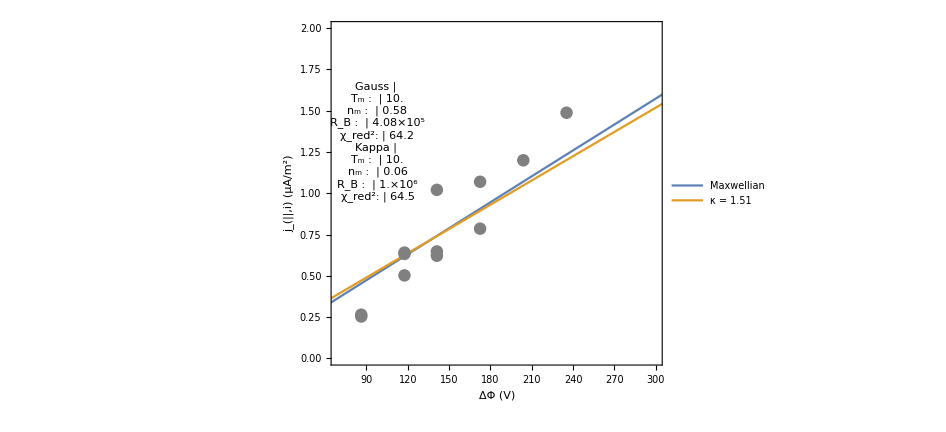

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

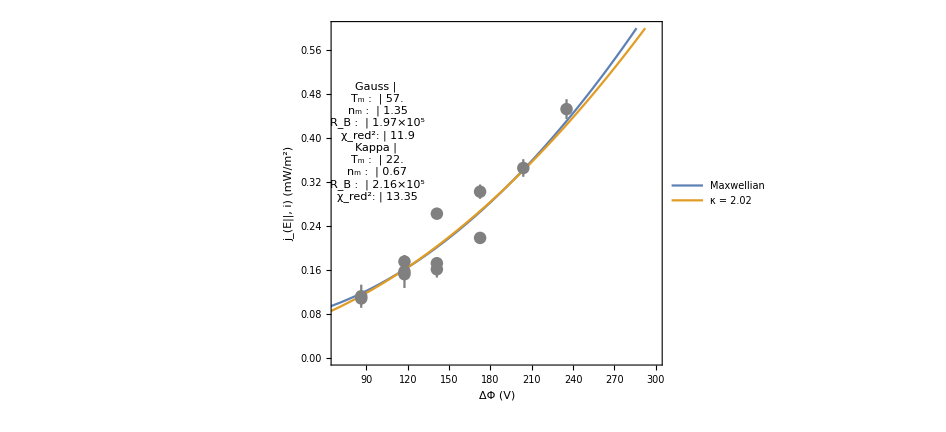

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

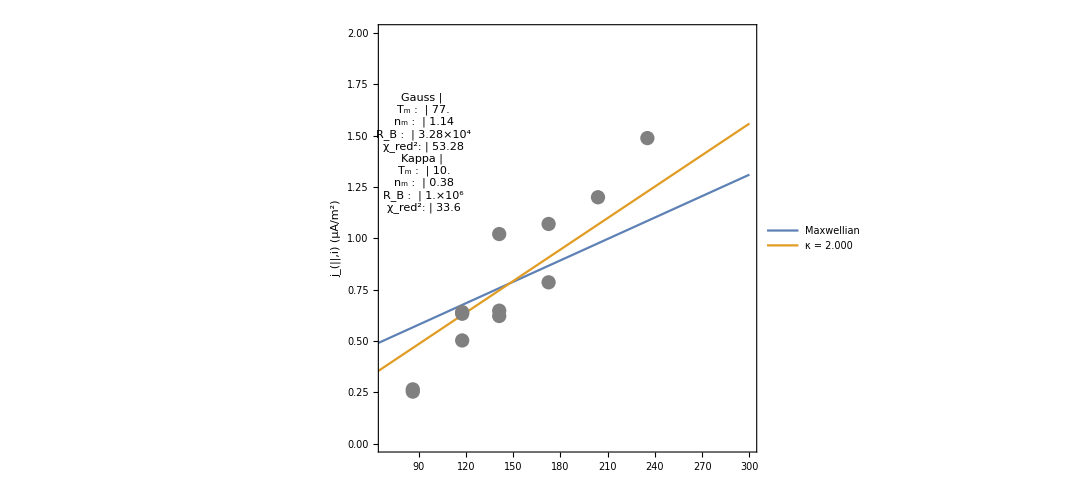
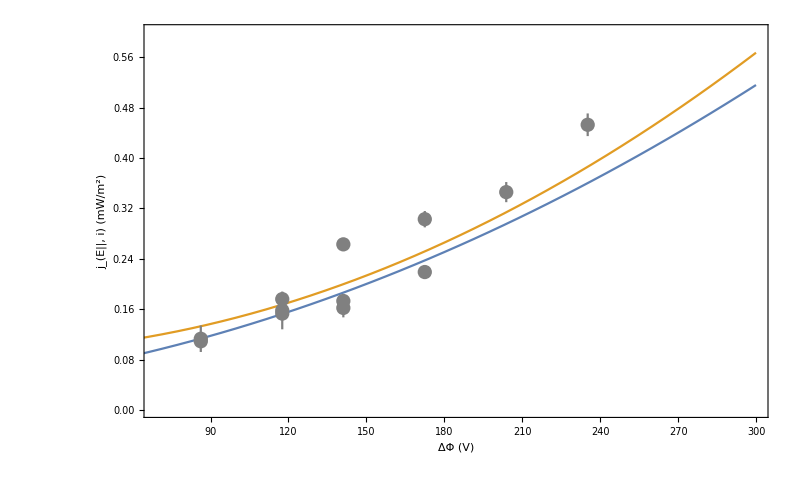

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180319/ ...

Orb11694__JeVFit__inds_162-198.png ...

Orb11694__combJVJeVFit__inds_162-198.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=5;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=Range[100,132];
```

```mathematica
indsSeg2=Range[137,150];
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[1+«18»])/((1-1/(«18»)) «1» Gamma[-1/2+«18»]),«4»,«1»,(0.0000268059 «6» Gamma[1+2.00683])/((-2+2.00683) (-1+2.00683) Gamma[-1/2+2.00683])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«1»,«4»,set==4,0.0000268059 0.103323 2900.27 («18»)^(3/2) (2+pot/5.00001-ⅇ^(-pot/((-1+2900.27) «18»)) (2 (1-1/2900.27)+pot/5.00001))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
doubledParTable1=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals1~Join~{""}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals2~Join~{""}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

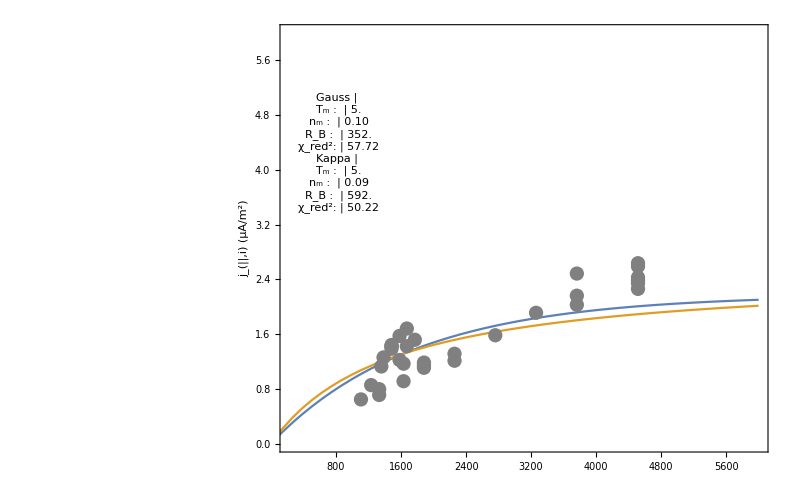
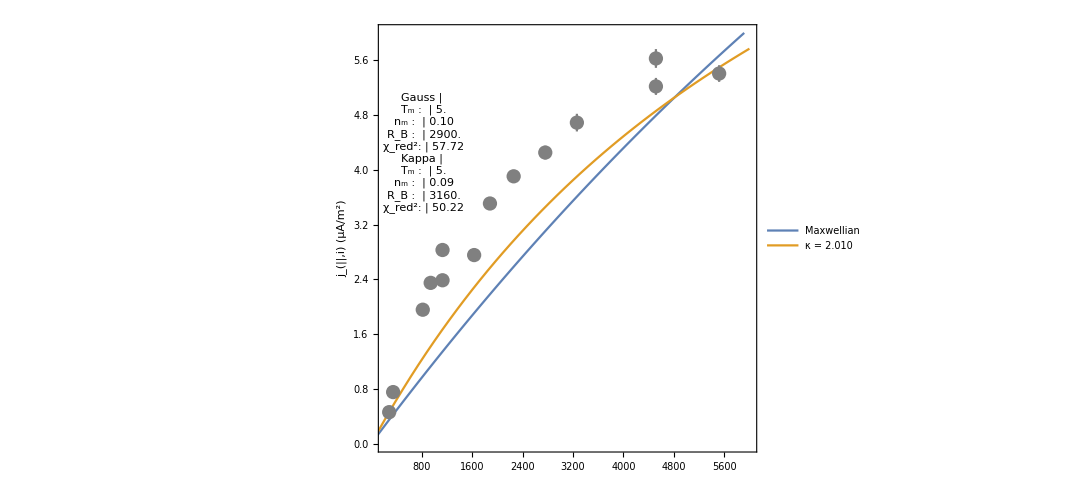
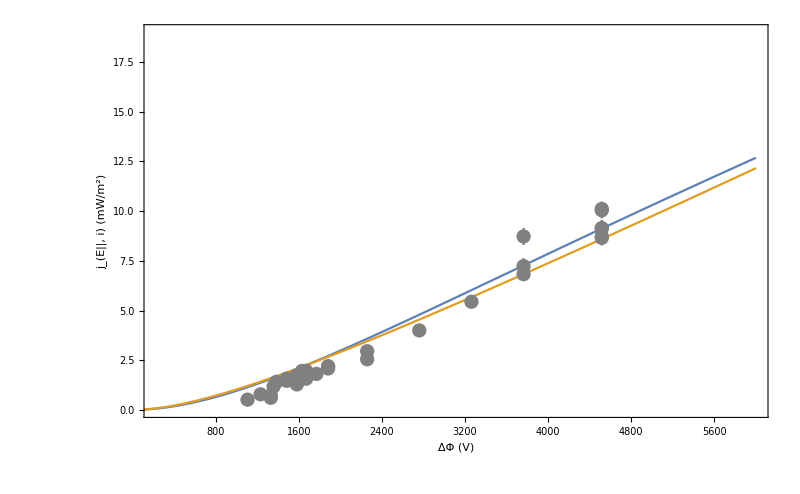
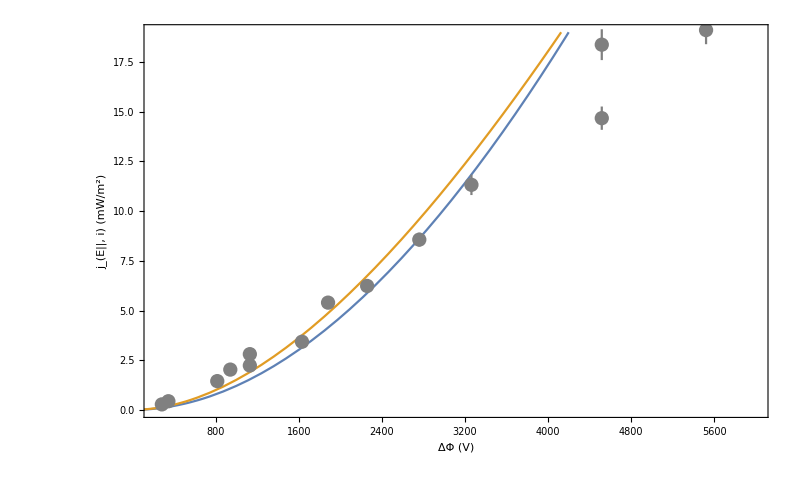
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,doubledJVPlot2},{doubledJeVPlot1,doubledJeVPlot2}}]
```

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503